PitchCallTotals has been added and produces some interesting observations on umpires. Let's look at the pitch calls form the Red Sox' first game of 2007.

```mathematica
PitchCallTotals[First[AllEvents["BOS",2007]]]
```

{56,102,123}

Tim Tschida called 56 strikes, 102 balls and 123 pitches needed no call (including intentional balls)

```mathematica
HomePlateUmpire[First[AllEvents["BOS",2007]]]
```

{tscht901,Tim Tschida}

Lets compute something more ambitious.  First lets identify all home plate umpire codes in 2007.

```mathematica
umps=Map[(HomePlateUmpire[#]//First)&,GameLogs[2007]]//Union
```

{barkl901,barrs901,barrt901,bellw901,buckc901,campa902,carlm901,cedeg901,coope901,cousd901,crawj901,culbf901,cuzzp901,danlk901,darlg901,davib902,davig901,delld901,demud901,diazl901,dimum901,dowda901,drakr901,drecb901,eddid901,emmep901,estam901,everm901,fairc901,fleta901,fostm901,froeb901,fullt901,gibsg901,gormb901,guccc901,hallt901,herna901,hicke901,hirsj901,hohnb901,holbs901,hoyej901,hudsm901,iassd901,johna901,joycj901,kellj901,knigb901,kulpr901,laynj901,marqa901,marsr901,mcclt901,mealj901,meric901,millb901,monte901,muchm901,nauep901,nelsj901,onorb901,poncl901,randt901,rapue901,reedr901,reilm901,reint901,relic901,reynj901,rungb901,schrp901,scotd901,ticht901,timmt901,tscht901,vanol901,wegnm901,welkb901,welkt901,wendh902,westj901,wintm901,wolfj901,younl901}

Now combine all of the regular season games from 2007 into one list.

```mathematica
Season2007=Union@@Map[Events[#,2007]&,TeamCodeListBasic[2007][[All,1]]];
```

This next expression takes some time to evaluate.  In it, we partition the games according to homeplate umpire and then add up the pitch calls for each umpire.  The numbers are not so informative, but the graphical display  below is interesting.

```mathematica
umpireCalls2007=Map[{HomePlateUmpire[First[#]],Total[Map[PitchCallTotals,#]]}&,SplitBy[SortBy[Season2007,HomePlateUmpire[#]&],HomePlateUmpire[#]&]]
```

({barkl901,Lance Barksdale} | {1737,3863,4680}
{barrs901,Scott Barry} | {366,1031,1131}
{barrt901,Ted Barrett} | {1789,3714,4650}
{bellw901,Wally Bell} | {1695,3621,4513}
{buckc901,CB Bucknor} | {1749,3789,4486}
{campa902,Angel Campos} | {285,670,868}
{carlm901,Mark Carlson} | {1733,3727,4686}
{cedeg901,Gary Cederstrom} | {1689,3393,4308}
{coope901,Eric Cooper} | {1590,3358,4248}
{cousd901,Derryl Cousins} | {1652,3580,4405}
{crawj901,Jerry Crawford} | {772,1776,2087}
{culbf901,Fieldin Culbreth} | {1636,3655,4543}
{cuzzp901,Phil Cuzzi} | {1791,3666,4585}
{danlk901,Kerwin Danley} | {1656,3619,4568}
{darlg901,Gary Darling} | {1678,3526,4420}
{davib902,Bob Davidson} | {1809,3697,4579}
{davig901,Gerry Davis} | {1692,4044,4835}
{delld901,Dusty Dellinger} | {50,93,114}
{demud901,Dana DeMuth} | {1746,3950,4686}
{diazl901,Laz Diaz} | {1861,3695,4916}
{dimum901,Mike DiMuro} | {464,947,1187}
{dowda901,Adam Dowdy} | {1404,2952,3676}
{drakr901,Rob Drake} | {1761,3878,4726}
{drecb901,Bruce Dreckman} | {1605,3288,4044}
{eddid901,Doug Eddings} | {1905,3369,4582}
{emmep901,Paul Emmel} | {1564,3082,3804}
{estam901,Mike Estabrook} | {147,315,433}
{everm901,Mike Everitt} | {1695,3525,4403}
{fairc901,Chad Fairchild} | {1451,3157,3877}
{fleta901,Andy Fletcher} | {889,1845,2426}
{fostm901,Marty Foster} | {1591,3337,4206}
{froeb901,Bruce Froemming} | {1754,3638,4575}
{fullt901,Troy Fullwood} | {94,191,272}
{gibsg901,Greg Gibson} | {1700,3985,4578}
{gormb901,Brian Gorman} | {1826,3742,4649}
{guccc901,Chris Guccione} | {2012,4467,5420}
{hallt901,Tom Hallion} | {1708,3602,4501}
{herna901,Angel Hernandez} | {1737,3945,4807}
{hicke901,Ed Hickox} | {1717,3650,4470}
{hirsj901,John Hirschbeck} | {1439,2771,3474}
{hohnb901,Bill Hohn} | {154,351,367}
{holbs901,Sam Holbrook} | {1795,3994,4779}
{hoyej901,James Hoye} | {1797,3875,4701}
{hudsm901,Marvin Hudson} | {1712,3670,4440}
{iassd901,Dan Iassogna} | {1736,3713,4566}
{johna901,Adrian Johnson} | {808,1762,2115}
{joycj901,Jim Joyce} | {1732,3776,4439}
{kellj901,Jeff Kellogg} | {1724,3805,4580}
{knigb901,Brian Knight} | {1414,3106,3837}
{kulpr901,Ron Kulpa} | {1842,3761,4780}
{laynj901,Jerry Layne} | {987,2287,2663}
{marqa901,Alfonso Marquez} | {1512,3340,4170}
{marsr901,Randy Marsh} | {1747,3988,4748}
{mcclt901,Tim McClelland} | {1809,3984,4989}
{mealj901,Jerry Meals} | {1592,3553,4313}
{meric901,Chuck Meriwether} | {1711,3794,4562}
{millb901,Bill Miller} | {1859,3691,4576}
{monte901,Ed Montague} | {1558,3495,4156}
{muchm901,Mike Muchlinski} | {340,734,814}
{nauep901,Paul Nauert} | {1789,3741,4768}
{nelsj901,Jeff Nelson} | {1093,2025,2427}
{onorb901,Brian O'Nora} | {962,1997,2390}
{poncl901,Larry Poncino} | {1542,3436,4355}
{randt901,Tony Randazzo} | {1695,3800,4619}
{rapue901,Ed Rapuano} | {1756,3749,4440}
{reedr901,Rick Reed} | {1770,3662,4471}
{reilm901,Mike Reilly} | {1727,3864,4659}
{reint901,Travis Reininger} | {269,552,712}
{relic901,Charlie Reliford} | {1344,2684,3339}
{reynj901,Jim Reynolds} | {1787,3862,4843}
{rungb901,Brian Runge} | {1809,3831,4732}
{schrp901,Paul Schrieber} | {1551,3729,4338}
{scotd901,Dale Scott} | {1952,3868,4691}
{ticht901,Todd Tichenor} | {242,529,605}
{timmt901,Tim Timmons} | {1610,3693,4351}
{tscht901,Tim Tschida} | {1691,3828,4768}
{vanol901,Larry Vanover} | {1816,3950,4901}
{wegnm901,Mark Wegner} | {1659,3663,4519}
{welkb901,Bill Welke} | {1798,3552,4483}
{welkt901,Tim Welke} | {1315,2779,3511}
{wendh902,Hunter Wendelstedt} | {1664,3584,4384}
{westj901,Joe West} | {1745,3886,4707}
{wintm901,Mike Winters} | {1620,3332,4081}
{wolfj901,Jim Wolf} | {1679,3438,4462}
{younl901,Larry Young} | {1073,2354,2925})

```mathematica
gamesByUmp=Map[{HomePlateUmpire[First[#]],#}&,SplitBy[SortBy[Season2007,HomePlateUmpire[#]&],HomePlateUmpire[#]&]];
```

```mathematica
pitchdata={#[[1]],Length[#[[2]]],Plus@@Map[PitchCallTotals,#[[2]]]}&/@gamesByUmp
```

({barkl901,Lance Barksdale} | 35 | {1737,3863,4680}
{barrs901,Scott Barry} | 8 | {366,1031,1131}
{barrt901,Ted Barrett} | 34 | {1789,3714,4650}
{bellw901,Wally Bell} | 33 | {1695,3621,4513}
{buckc901,CB Bucknor} | 34 | {1749,3789,4486}
{campa902,Angel Campos} | 6 | {285,670,868}
{carlm901,Mark Carlson} | 34 | {1733,3727,4686}
{cedeg901,Gary Cederstrom} | 33 | {1689,3393,4308}
{coope901,Eric Cooper} | 32 | {1590,3358,4248}
{cousd901,Derryl Cousins} | 33 | {1652,3580,4405}
{crawj901,Jerry Crawford} | 16 | {772,1776,2087}
{culbf901,Fieldin Culbreth} | 34 | {1636,3655,4543}
{cuzzp901,Phil Cuzzi} | 35 | {1791,3666,4585}
{danlk901,Kerwin Danley} | 34 | {1656,3619,4568}
{darlg901,Gary Darling} | 33 | {1678,3526,4420}
{davib902,Bob Davidson} | 34 | {1809,3697,4579}
{davig901,Gerry Davis} | 35 | {1692,4044,4835}
{delld901,Dusty Dellinger} | 1 | {50,93,114}
{demud901,Dana DeMuth} | 34 | {1746,3950,4686}
{diazl901,Laz Diaz} | 36 | {1861,3695,4916}
{dimum901,Mike DiMuro} | 9 | {464,947,1187}
{dowda901,Adam Dowdy} | 27 | {1404,2952,3676}
{drakr901,Rob Drake} | 35 | {1761,3878,4726}
{drecb901,Bruce Dreckman} | 30 | {1605,3288,4044}
{eddid901,Doug Eddings} | 34 | {1905,3369,4582}
{emmep901,Paul Emmel} | 29 | {1564,3082,3804}
{estam901,Mike Estabrook} | 3 | {147,315,433}
{everm901,Mike Everitt} | 34 | {1695,3525,4403}
{fairc901,Chad Fairchild} | 28 | {1451,3157,3877}
{fleta901,Andy Fletcher} | 18 | {889,1845,2426}
{fostm901,Marty Foster} | 31 | {1591,3337,4206}
{froeb901,Bruce Froemming} | 33 | {1754,3638,4575}
{fullt901,Troy Fullwood} | 2 | {94,191,272}
{gibsg901,Greg Gibson} | 34 | {1700,3985,4578}
{gormb901,Brian Gorman} | 34 | {1826,3742,4649}
{guccc901,Chris Guccione} | 40 | {2012,4467,5420}
{hallt901,Tom Hallion} | 33 | {1708,3602,4501}
{herna901,Angel Hernandez} | 36 | {1737,3945,4807}
{hicke901,Ed Hickox} | 34 | {1717,3650,4470}
{hirsj901,John Hirschbeck} | 26 | {1439,2771,3474}
{hohnb901,Bill Hohn} | 3 | {154,351,367}
{holbs901,Sam Holbrook} | 34 | {1795,3994,4779}
{hoyej901,James Hoye} | 35 | {1797,3875,4701}
{hudsm901,Marvin Hudson} | 32 | {1712,3670,4440}
{iassd901,Dan Iassogna} | 34 | {1736,3713,4566}
{johna901,Adrian Johnson} | 16 | {808,1762,2115}
{joycj901,Jim Joyce} | 34 | {1732,3776,4439}
{kellj901,Jeff Kellogg} | 35 | {1724,3805,4580}
{knigb901,Brian Knight} | 28 | {1414,3106,3837}
{kulpr901,Ron Kulpa} | 35 | {1842,3761,4780}
{laynj901,Jerry Layne} | 19 | {987,2287,2663}
{marqa901,Alfonso Marquez} | 31 | {1512,3340,4170}
{marsr901,Randy Marsh} | 35 | {1747,3988,4748}
{mcclt901,Tim McClelland} | 37 | {1809,3984,4989}
{mealj901,Jerry Meals} | 32 | {1592,3553,4313}
{meric901,Chuck Meriwether} | 33 | {1711,3794,4562}
{millb901,Bill Miller} | 34 | {1859,3691,4576}
{monte901,Ed Montague} | 31 | {1558,3495,4156}
{muchm901,Mike Muchlinski} | 7 | {340,734,814}
{nauep901,Paul Nauert} | 35 | {1789,3741,4768}
{nelsj901,Jeff Nelson} | 20 | {1093,2025,2427}
{onorb901,Brian O'Nora} | 18 | {962,1997,2390}
{poncl901,Larry Poncino} | 32 | {1542,3436,4355}
{randt901,Tony Randazzo} | 33 | {1695,3800,4619}
{rapue901,Ed Rapuano} | 34 | {1756,3749,4440}
{reedr901,Rick Reed} | 33 | {1770,3662,4471}
{reilm901,Mike Reilly} | 34 | {1727,3864,4659}
{reint901,Travis Reininger} | 5 | {269,552,712}
{relic901,Charlie Reliford} | 25 | {1344,2684,3339}
{reynj901,Jim Reynolds} | 35 | {1787,3862,4843}
{rungb901,Brian Runge} | 36 | {1809,3831,4732}
{schrp901,Paul Schrieber} | 31 | {1551,3729,4338}
{scotd901,Dale Scott} | 35 | {1952,3868,4691}
{ticht901,Todd Tichenor} | 5 | {242,529,605}
{timmt901,Tim Timmons} | 33 | {1610,3693,4351}
{tscht901,Tim Tschida} | 35 | {1691,3828,4768}
{vanol901,Larry Vanover} | 36 | {1816,3950,4901}
{wegnm901,Mark Wegner} | 33 | {1659,3663,4519}
{welkb901,Bill Welke} | 34 | {1798,3552,4483}
{welkt901,Tim Welke} | 25 | {1315,2779,3511}
{wendh902,Hunter Wendelstedt} | 33 | {1664,3584,4384}
{westj901,Joe West} | 36 | {1745,3886,4707}
{wintm901,Mike Winters} | 32 | {1620,3332,4081}
{wolfj901,Jim Wolf} | 33 | {1679,3438,4462}
{younl901,Larry Young} | 21 | {1073,2354,2925})

```mathematica
StrikeBallPoint[{a_,b_,c_}]:={a,b}/(a+b+c)//N
```

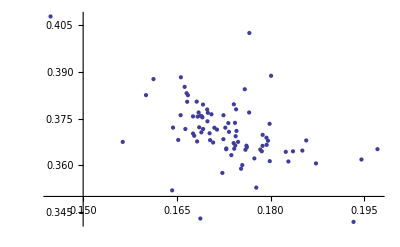

```mathematica
Map[Tooltip[StrikeBallPoint[#[[3]]],{#[[1]],#[[2]]}]&,pitchdata]//ListPlot
```

```mathematica
StrikePercentage[{a_,b_,c_}]:=N[a/(a+b)]
```

```mathematica
Map[{#[[1,2]],#[[2]],StrikePercentage[#[[3]]]}&,pitchdata]//SortBy[#,Last]&//Select[#,#[[2]]≥10&]&
```

(Paul Schrieber | 31 | 0.29375
Gerry Davis | 35 | 0.294979
Greg Gibson | 34 | 0.299033
Jerry Layne | 19 | 0.301466
Jerry Crawford | 16 | 0.302983
Tim Timmons | 33 | 0.303602
Randy Marsh | 35 | 0.304621
Angel Hernandez | 36 | 0.305702
Tim Tschida | 35 | 0.306396
Dana DeMuth | 34 | 0.306531
Ed Montague | 31 | 0.308332
Tony Randazzo | 33 | 0.308462
Mike Reilly | 34 | 0.308889
Fieldin Culbreth | 34 | 0.309204
Jerry Meals | 32 | 0.309427
Larry Poncino | 32 | 0.309763
Joe West | 36 | 0.309892
Sam Holbrook | 34 | 0.310071
Lance Barksdale | 35 | 0.310179
Chris Guccione | 40 | 0.310542
Chuck Meriwether | 33 | 0.310808
Alfonso Marquez | 31 | 0.311624
Mark Wegner | 33 | 0.311725
Jeff Kellogg | 35 | 0.31181
Tim McClelland | 37 | 0.312273
Rob Drake | 35 | 0.312289
Brian Knight | 28 | 0.312832
Larry Young | 21 | 0.313102
Kerwin Danley | 34 | 0.313934
Adrian Johnson | 16 | 0.314397
Jim Joyce | 34 | 0.314452
Chad Fairchild | 28 | 0.314887
Larry Vanover | 36 | 0.31495
Derryl Cousins | 33 | 0.315749
CB Bucknor | 34 | 0.315818
Jim Reynolds | 35 | 0.316339
James Hoye | 35 | 0.316819
Hunter Wendelstedt | 33 | 0.317073
Mark Carlson | 34 | 0.317399
Marvin Hudson | 32 | 0.318097
Dan Iassogna | 34 | 0.318591
Wally Bell | 33 | 0.318849
Ed Rapuano | 34 | 0.318983
Ed Hickox | 34 | 0.319918
Brian Runge | 36 | 0.320745
Tim Welke | 25 | 0.321202
Eric Cooper | 32 | 0.321342
Tom Hallion | 33 | 0.321657
Adam Dowdy | 27 | 0.322314
Gary Darling | 33 | 0.322444
Marty Foster | 31 | 0.322849
Paul Nauert | 35 | 0.323508
Mike Everitt | 34 | 0.324713
Ted Barrett | 34 | 0.325095
Brian O'Nora | 18 | 0.32511
Andy Fletcher | 18 | 0.325165
Bruce Froemming | 33 | 0.325297
Rick Reed | 33 | 0.325847
Mike Winters | 32 | 0.327141
Brian Gorman | 34 | 0.327945
Bruce Dreckman | 30 | 0.32802
Jim Wolf | 33 | 0.328122
Phil Cuzzi | 35 | 0.328202
Bob Davidson | 34 | 0.328551
Ron Kulpa | 35 | 0.328752
Gary Cederstrom | 33 | 0.332349
Charlie Reliford | 25 | 0.333664
Laz Diaz | 36 | 0.334953
Bill Miller | 34 | 0.334955
Dale Scott | 35 | 0.335395
Bill Welke | 34 | 0.336075
Paul Emmel | 29 | 0.336634
John Hirschbeck | 26 | 0.341805
Jeff Nelson | 20 | 0.350545
Doug Eddings | 34 | 0.361206)